# Exercise 16

As with all of the exercises you will complete in this course, you will be expected to turn your *.nb file in to the course TA before the next lecture.  Please do so by e-mailing your completed exercise file to Lan Yu (ece329.uiuc@gmail.com), make sure you name the file using the following notation: “Exn_Last_First.nb”, where n is the Exercise number (in this case, 16), and First and Last would be your first and last name.  So my submission to Lan for this exercise would be titled “Ex16_Wasserman_Dan.nb”.  You will receive full credit for your exercise if it turned in before the next lecture (Lecture n+1).  No late submissions will be accepted.

## Objective/Overview:

In today’s Lecture (16) we discussed a number of very important concepts, including the displacement current ((∂D⃗)/(∂t)) and charge conservation  and the continuity equation ((∂ρ)/(∂t)=-∇·J⃗).  We also introduced the concept of bound currents and their relationship to a material’s permeability.  In this exercise, we will dig a little deeper in the concept of magnetization and permeability.

## Magnetic Susceptibility

At the end of our lecture today we presented Maxwell’s Equations as they are most commonly used: where the microscopic effects from bound charges are wrapped up into the permittivity.  We like these Maxwell’s Equations because with them, we don’t have to worry about every single proton and electron in our material.
∇·D⃗=ρ_free  Gauss’s Law
∇·B⃗=0 No Magnetic Monopoles
∇×E⃗=-(ⅆ B⃗)/ⅆt Faraday’s Law
∇×H⃗=J⃗+(ⅆ D⃗)/ⅆt  Ampere’s Law, where J⃗ includes contributions from ALL currents, free and bound
with D⃗=ϵ E⃗ and B⃗=μ_o H⃗ 
We acknowledged that our J⃗ can have both bound and free charge components, and we wrote J⃗=(J⃗)_free+∇×M⃗, so our Ampere’s Law now becomes:
∇×H⃗=(J⃗)_free+∇×M⃗+(ⅆ D⃗)/ⅆt , B⃗=μ_o H⃗
Which we can re-write as
∇×((B⃗)/μ_o-M⃗)=(J⃗)_free+(ⅆ D⃗)/ⅆt 
We can now get a definition for H⃗ which depends on the Magnetization field M⃗, in the same way that our D⃗ depends onf our polarization field P⃗
H⃗=((B⃗)/μ_o-M⃗)
If the degree of Magnetization of the material is proportional to the H⃗ field, M⃗=χ_m H⃗, we can write:
B⃗=μ_o(H⃗+χ_m H⃗)=μ_o(1+χ_m)H⃗=μ H⃗=μ_o μ_rH⃗
In the same way that an external electric field induces a polarization of a dielectric, which in turn, creates a polarization field that changes the total electric field in the material, a magnetic field can induce bound current loops in our material, which create an internal magnetic field, which will also change the total magnetic field in our material.
Let’s try to understand this with a simple model.  We will assume we have a wire on the z axis, carrying a current I=2π/μ_o.  We start by assuming the wire is floating in air, and from our NEW Ampere’s Law ∮H⃗·dl⃗=I_enc we can solve for H⃗.  The figure below shows the 3 situations we will study in this exercise.
-Graphics-

```mathematica
muo=1.2566*10^-6;
```

```mathematica
hwire1cyl=1/(muo*r)
```

795798./r

```mathematica
hwire1=TransformedField["Polar"->"Cartesian",{0,hwire1cyl},{r,θ}->{x,y}]
```

{-(795798. y)/(x^2+y^2),(795798. x)/(x^2+y^2)}

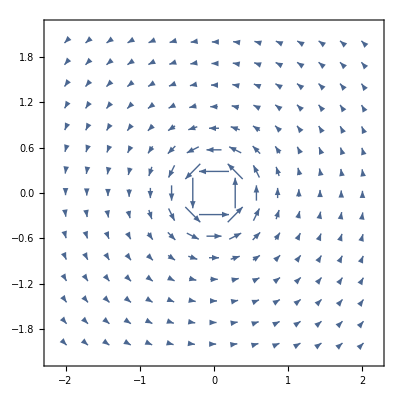

```mathematica
VectorPlot[Boole[x^2+y^2≥ 0.05]*{-(795798.185580137 y)/(x^2+y^2),(795798.185580137 x)/(x^2+y^2)},{x,-2,2},{y,-2,2}]
```

The B field will simply be, for a wire surrounded by air,  B⃗=μ_o H⃗

```mathematica
bwire1=TransformedField["Polar"->"Cartesian",{0,muo*hwire1cyl},{r,θ}->{x,y}]
```

{-(1. y)/(x^2+y^2),(1. x)/(x^2+y^2)}

```mathematica
VectorPlot[Boole[x^2+y^2≥  0.05]*bwire1,{x,-2,2},{y,-2,2},PlotRange->Full ]
```

-Graphics-

## Diamagnetic Materials

Now let’s see what happens when we introduce a cylindrical shell of magnetic material around our wire, from r=1 to r=2.  A magentic material is defined by its magnetic susceptibility.  For a diamagnetic material, χ_m<0, where |χ_m|<<1.  Let’s exaggerate and say that χ_m=-0.5.  This means that   μ=μ_o(1+χ_m)=μ_o/2.  If we look at Ampere’s Law, we can see that it doesn’t change at all!

```mathematica
hwirediamag=hwire1
```

{-(795798. y)/(x^2+y^2),(795798. x)/(x^2+y^2)}

But our B field will change in the region between r=1 and r=2.  So let’s define a mudiamag, this is our permeability as a function of position

```mathematica
mudiamag=muo*If[1≤ x^2+y^2≤4,0.5,1]
```

1.2566×10^-6 If[1≤x^2+y^2≤4,0.5,1]

```mathematica
bwirediamag=mudiamag*hwirediamag
```

{-(1. y If[1≤x^2+y^2≤4,0.5,1])/(x^2+y^2),(1. x If[1≤x^2+y^2≤4,0.5,1])/(x^2+y^2)}

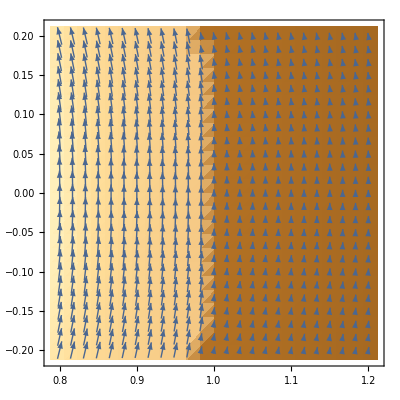

```mathematica
VectorDensityPlot[bwirediamag,{x,.8,1.2},{y,-.2,.2},PlotRange->Full ,VectorPoints->Fine]
```

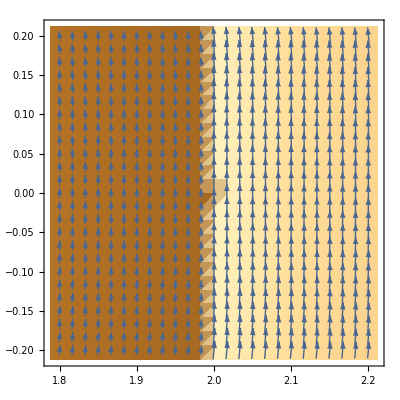

```mathematica
VectorDensityPlot[bwirediamag,{x,1.8,2.2},{y,-.2,.2},PlotRange->Full ,VectorPoints->Fine]
```

Let’s plot B(r)

```mathematica
bwirediamagr=-(Piecewise[{{1, r<1}, {0.5, 1≤r^2≤4}, {1, r>2}, {0, True}}])/r
```

-Piecewise[{{1, r<1}, {0.5, 1≤r^2≤4}, {1, r>2}, {0, True}}]/r

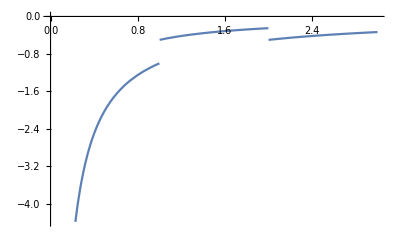

```mathematica
Plot[%,{r,0,3}]
```

You should notice that the tangential component of the B field, unlike your H field, is NOT continuous at the interfaces between air and your magnetic material!

## Paramagnetic Materials

For a paramagnetic material, χ_m>0, where |χ_m|<<1.  Let’s exaggerate and say that χ_m=0.8.  This means that   μ=μ_o(1+χ_m)=1.8 μ_o. Calculate and plot the H and B fields for this system, as well as B(r).  Follow the approach we used for the diamagnetic material, except that you will need to define a new term muparamag, to replace the mudiamag you used earlier.

```mathematica
muparamag=muo*If[1≤ x^2+y^2≤4,1.8,1]
```

1.2566×10^-6 If[1≤x^2+y^2≤4,1.8,1]

```mathematica
bwireparamag=muparamag*hwirediamag
```

{-(1. y If[1≤x^2+y^2≤4,1.8,1])/(x^2+y^2),(1. x If[1≤x^2+y^2≤4,1.8,1])/(x^2+y^2)}

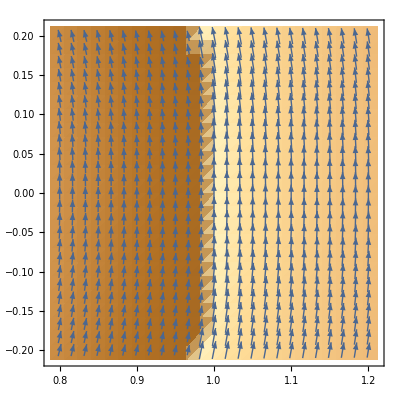

```mathematica
VectorDensityPlot[bwireparamag,{x,.8,1.2},{y,-.2,.2},PlotRange->Full ,VectorPoints->Fine]
```

```mathematica
bwireparamagr=-(Piecewise[{{1, r<1}, {1.8, 1≤r≤2}, {1, r>2}, {0, True}}])/r
```

-Piecewise[{{1, r<1}, {1.8, 1≤r≤2}, {1, r>2}, {0, True}}]/r

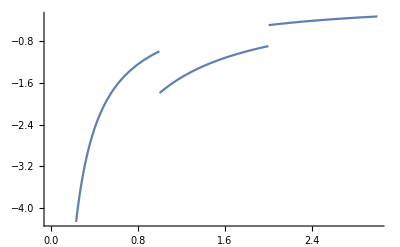

```mathematica
Plot[bwireparamagr,{r,0,3}]
```

Again, what do you notice about the B field that is different than the H field?

## Ferromagnetic Materials

Ferromagnetic materials are the materials we generally refer to as “magnetic”.  They include Iron, Nickel, Cobalt, etc.  For these materials, the relationship between H and B is more complicated, as the magnetic susceptibility can be nonlinear in applied B field, in both amplitude AND time. For this reason, developing a model of a material’s ferromagnetism is quite complicated, and ultimately relies on a quantum mechanical calculation.

## Boundary Conditions

One more thing...  We have already seen, in our Vector plots, that at the surface of a material with μ≠μ_o (and NO SURFACE CURRENT), the tangential component of H is continuous, and the tangential component of B is discontinuous.  These are half of the boundary conditions for magnetic fields.  Let’s see what happens when we remove our shell, and instead fill all of space x>0 with a paramagnetic material.  To do this, we need to go back to Ampere’s Law.
-Graphics-
∮_1 (H⃗)_1·dl⃗+∮_2 (H⃗)_2·d l⃗=I_enc, where H⃗=Piecewise[{{(H⃗)_1, x>0}, {(H⃗)_2, x<0}}].  The normal component of B MUST be continuous at the interface, otherwise ∇·B⃗≠0!  This tells us that (1/μ_1+1/μ_2)B(r)2πr=I_enc.  So
B(r)=((μ_1 μ_2)/(μ_1+μ_2))×1/(μ_o r)
Let’s plot B(r) then, assuming our paramagnetic material has χ_m=0.8

```mathematica
bwire2cyl=(1*muo*1.8*muo/(1.8*muo+1*muo))/(muo*r)
```

0.642857/r

```mathematica
bwire2xyz=TransformedField["Polar"->"Cartesian",{0,bwire2cyl},{r,θ}->{x,y}]
```

{-(0.642857 y)/(x^2+y^2),(0.642857 x)/(x^2+y^2)}

```mathematica
VectorPlot[Boole[x^2+y^2≥  0.05]*bwire2xyz,{x,-2,2},{y,-2,2}]
```

-Graphics-

OK, now calculate H for this system.  What do you see about the NORMAL component of H at a boundary?  Is it continuous, does it change?

```mathematica
hwire2xyz=If[x>0,bwire2xyz/(muo*1.8),bwire2xyz/muo]
```

If[x>0,bwire2xyz/(muo 1.8),bwire2xyz/muo]

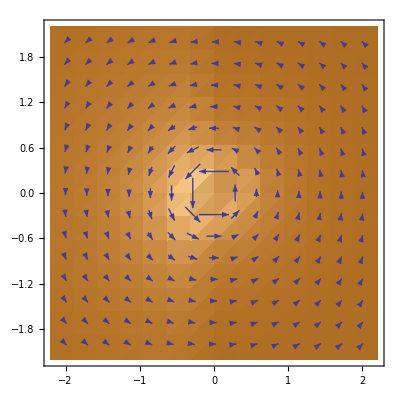

```mathematica
VectorDensityPlot[Boole[x^2+y^2≥  0.05]*hwire2xyz,{x,-2,2},{y,-2,2}]
```

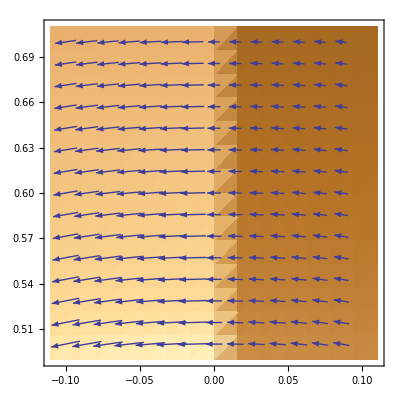

```mathematica
VectorDensityPlot[Boole[x^2+y^2≥  0.05]*hwire2xyz,{x,-.1,.1},{y,.5,.7}]
```